```mathematica
Clear["Global`*"];

(*References in UE4: 
 GetSimpleForwardLightingDirectionalLight
EvaluateBxDF
IntegrateBxDF
DefaultLitBxDF
SpecularGGX
*)
DGGX[m_,NoH_]:=m^2/(π*((NoH^2*(m^2-1))+1)^2);

VisSmithG[m_,x_]:=x+Sqrt[m^2+(1-m^2)*x^2];
VisSmith[m_,NoL_,NoV_]:=1/(VisSmithG[m,NoL]*VisSmithG[m,NoV]);

FresnelOriginN[SpecularColor_]:=(1+Sqrt[Max[SpecularColor,0.99]])/(1-Max[SpecularColor,0.99]);
FresnelOriginG[VoH_,SpecularColor_]:=Sqrt[FresnelOriginN[SpecularColor]^2+VoH^2-1];
FresnelOrigin[VoH_,SpecularColor_]:=0.5*((FresnelOriginG[VoH,SpecularColor]-VoH)/(FresnelOriginG[VoH,SpecularColor]+VoH))^2*(1+(((FresnelOriginG[VoH,SpecularColor]+VoH)*VoH-1)/((FresnelOriginG[VoH,SpecularColor]-VoH)*VoH+1))^2);

BRDF[m_,normalDir_,lightDir_,viewDir_,specularColor_]:=Module[
{normal,light,view,half,NoL,NoV,NoH,VoH,D,Vis,F},
normal=Normalize[normalDir];
light=Normalize[lightDir];
view=Normalize[viewDir];
half=Normalize[(view+light)/2];
NoL=Clip[Dot[normal,light],{0,1}];
NoV=Dot[normal,view];
NoH=Dot[normal,half];
VoH=Dot[view,half];

D=DGGX[m,NoH];
Vis=VisSmith[m,NoL,NoV];
F=FresnelOrigin[VoH,specularColor];
D*Vis*F
];

BRDF2[m_,normalDir_,lightDir_,viewDir_]=BRDF[m,normalDir,lightDir,viewDir,0.99];

BRDF3[m_,normalAngle_,lightAngle_,viewAngle_]:=Module[
{normalDir,lightDir,viewDir},
normalDir=FromPolarCoordinates[{1,normalAngle}];
lightDir=FromPolarCoordinates[{1,lightAngle}];
viewDir=FromPolarCoordinates[{1,viewAngle}];
BRDF2[m,normalDir,lightDir,viewDir]
];

(*normal: π/2, view: π/4*)
BRDF4[m_,lightAngle_]=BRDF3[m,π/2,lightAngle,π/4];

(*normal: π/2, view: π/4*)
BRDF5[m_,lightAngle_]:=If[0≤lightAngle≤π,BRDF4[m,lightAngle],0];

Print[">BRDF: D*G*F/(4*NoL*NoV)=D*Vis*F"];
BRDF4[0.5,3π/4]
```

>BRDF: D*G*F/(4*NoL*NoV)=D*Vis*F

0.555711

```mathematica
BRDFLighting[m_,normalAngle_,lightAngle_,viewAngle_]:=Module[
{NoL=Max[0,Cos[lightAngle-normalAngle]]},
NoL*BRDF3[m,normalAngle,lightAngle,viewAngle]];
BRDFLighting[0.2,π/2,3π/4,π/4]
```

2.75859

```mathematica
Print[">BRDF(light angle offset): normal: π/2, view: π/4"];
Manipulate[Plot[BRDFLighting[roughness,π/2,lightAngle+lightAngleOffset,π/4],
{lightAngleOffset,-π,π}, PlotRange->{{-3.5,3.5},{-0.1,2}},AspectRatio->1],
{roughness,0.2,0.9},{lightAngle,π/2,π}]
```

>BRDF(light angle offset): normal: π/2, view: π/4

1.72058 >Integrated BRDF:

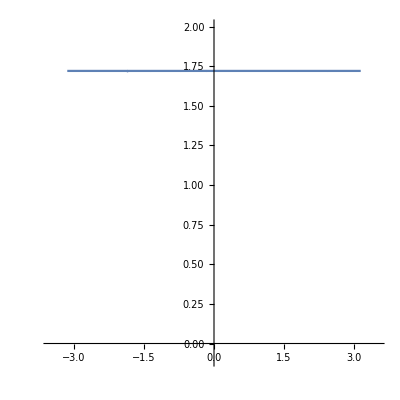

```mathematica
lightPower[lightAngle_]=1;
BRDFIntegral[m_,normalAngle_,lightAngle_,viewAngle_]:=Module[
{lightAngleOffset},
NIntegrate[lightPower[lightAngle+lightAngleOffset]* BRDFLighting[m,normalAngle,lightAngle+lightAngleOffset,viewAngle],{lightAngleOffset,-π,π},PrecisionGoal->3,WorkingPrecision->3]];

Print[">Integrated BRDF:" BRDFIntegral[0.2,π/2,3π/4,π/4]];
Plot[BRDFIntegral[0.2,π/2,lightAngle,π/4],
{lightAngle,-π,π}, PlotRange->{{-3.5,3.5},{-0.1,2}},AspectRatio->1]
```